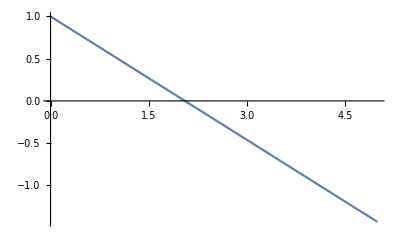

```mathematica
h=1.05*10^-34;(*1.05*10^-34*)
T = 10;
β=1/(1.38×10^-23*T);(*1/(1.38×10^-23*T)*)
m=4*1.66*10^(-27);(*9.1*10^-31*)
μ0=9*10^4;
ee=1.6*10^(-19);
k=1.38×10^-23;
ncritt[T_]:=(4π)/(2*π*h)^3*(√(π/2)*Zeta[3/2])/(1/(m*k*T))^(3/2);
tcrit[μ_]:=1/k*h^2/m*n[μ,10]^(2/3)
n[μ_,T_]:=NIntegrate[(4*π*p^2)/(2*π*h)^3*1/(ⅇ^(1/(k*T)*(p^2/(2*m)-μ))-1),{p,0,10^(-23)}]
ϵ[μ_,T_]:=NIntegrate[(4*π*p^2)/(2*π*h)^3*(p^2/(2*m))/(ⅇ^(1/(k*T)*(p^2/(2*m)-μ))-1),{p,0,10^(-23)}]
eclass[μ_,T_]:=(3n[μ,10])/2*k*T
eratio[n_]:=(Zeta[5/2]/Zeta[3/2]-1)*n+1
Plot[eratio[n],{n,0,5}]
```

```mathematica
""
```

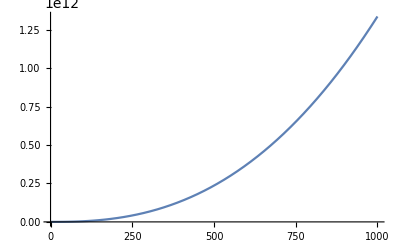

```mathematica
Plot[3/2 * ncritt[T]*k*T*Zeta[5/2]/Zeta[3/2],{T,0, 1000}]
```

2.94572

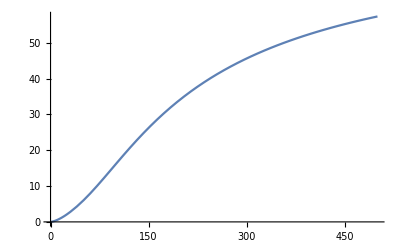

```mathematica
po= -10^(-25);
tcrit[po]
Plot[ϵ[po, T]/eclass[po,T], {T,0,500}]
```

```mathematica
delta = 0.001
```

0.001

```mathematica
delta = 0.001
```

0.001

1.×10^-8

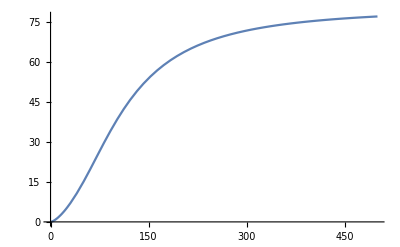

ND[x,x,2]

```mathematica
po= -10^(-25);
delta = 0.00000001
Plot[(ϵ[po, T+delta]-ϵ[po, T])/(delta*(eclass[po,T]/T)), {T,0,500}]
```